```mathematica
imgsize=800;
SetDirectory@NotebookDirectory[];
```

Tools

Unit converter

Convert eV^(-1) to km

```mathematica
eVInvert2km[eVInvert_]:=eVInvert*1.97*10^(-10);
```

```mathematica
km2eVInvert[km_]:=km/(1.97*10^(-10));
```

Resonance Width

In the explaination using the approximation of Bessel functions, I mentioned α should be large (perturbation amplitude A should be small). Then how large is large? (How small is small?)

```mathematica
Reduce[Sech[x]==amp,x]
```

C[1]∈ℤ&&amp≠0&&(x==-ArcCosh[1/amp]+2 ⅈ π C[1]||x==ArcCosh[1/amp]+2 ⅈ π C[1])

```mathematica
alpha[amp_]:=ArcCosh[1/amp]
```

```mathematica
alpha[0.1]
```

2.99322

```mathematica
Series[Tanh[x],{x,0,5}]
```

x-x^3/3+(2 x^5)/15+O[x]^6

```mathematica
Tanh[x]-x/.{x->}
```

0

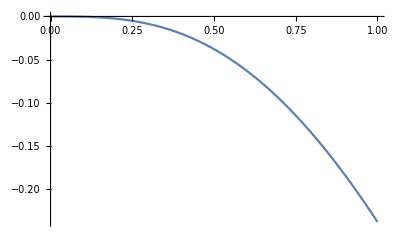

```mathematica
Plot[Tanh[x]-x,{x,0,1}]
```

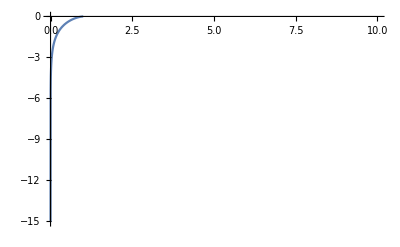

```mathematica
Plot[Tanh[alpha[amp]]-alpha[amp],{amp,0,10},PlotRange->Full]
```

```mathematica
rabisys=I D[{rabi1[x],rabi2[x]},x]=={{-omega/2,w Exp[I k x]},{w Exp[I k x],omega/2}}.{rabi1[x],rabi2[x]}
```

{ⅈ rabi1'[x],ⅈ rabi2'[x]}=={-1/2 omega rabi1[x]+ⅇ^(ⅈ k x) w rabi2[x],ⅇ^(ⅈ k x) w rabi1[x]+1/2 omega rabi2[x]}

```mathematica
rabiinit={rabi1[0],rabi2[0]}=={1,0}
```

{rabi1[0],rabi2[0]}=={1,0}

```mathematica
DSolve[rabisys&&rabiinit,{rabi1,rabi2},x]
```

DSolve[{ⅈ rabi1'[x],ⅈ rabi2'[x]}=={-1/2 omega rabi1[x]+ⅇ^(ⅈ k x) w rabi2[x],ⅇ^(ⅈ k x) w rabi1[x]+1/2 omega rabi2[x]}&&{rabi1[0],rabi2[0]}=={1,0},{rabi1,rabi2},x]

Reproduce Vacuum Oscillation Plots

Damn has to use the original values

```mathematica
theta12=33.36/180*Pi;
theta13=8.66/180*Pi;
theta23=40/180*Pi;
deltacp=0;
(*deltacp=300/180*Pi;*)
m1sq=0.01;
m2sq=m1sq+0.000079;
m3sq=m2sq+0.0027;
m3sqIH=m2sq-0.0027;
energy=10^(6);(*1MeV*)
```

The PMNS matrix is

```mathematica
pmns={{Cos[theta12]Cos[theta13],Sin[theta12]Cos[theta13],Sin[theta13]Exp[-I deltacp]},{-Sin[theta12]Cos[theta23]-Cos[theta12]Sin[theta23]Sin[theta13]Exp[I deltacp],Cos[theta12]Cos[theta23]-Sin[theta12]Sin[theta23]Sin[theta13]Exp[I deltacp],Sin[theta23]Cos[theta13]},{Sin[theta12]Sin[theta23]-Cos[theta12]Cos[theta23]Sin[theta13]Exp[I deltacp],-Cos[theta12]Sin[theta23]-Sin[theta12]Cos[theta23]Sin[theta13]Exp[I deltacp],Cos[theta23]Cos[theta13]}}
%//MatrixForm
```

{{0.82571,0.543629,0.150571},{-0.502084,0.586603,0.635459},{0.257129,-0.600304,0.757311}}

(0.82571 | 0.543629 | 0.150571
-0.502084 | 0.586603 | 0.635459
0.257129 | -0.600304 | 0.757311)

```mathematica
hamilVac=1/(2 energy)pmns.{{m1sq,0,0},{0,m2sq,0},{0,0,m3sq}}.Transpose[pmns];
hamilVacIH=1/(2 energy)pmns.{{m1sq,0,0},{0,m2sq,0},{0,0,m3sqIH}}.Transpose[pmns];
```

```mathematica
nuVac[x_]={nuVace[x],nuVacm[x],nuVact[x]}
```

{nuVace[x],nuVacm[x],nuVact[x]}

```mathematica
vacOsc = I nuVac'[x]==hamilVac.nuVac[x]
vacOscIH = I nuVac'[x]==hamilVacIH.nuVac[x]
```

{ⅈ nuVace'[x],ⅈ nuVacm'[x],ⅈ nuVact'[x]}=={5.04318×10^-9 nuVace[x]+1.45546×10^-10 nuVacm[x]+1.45553×10^-10 nuVact[x],1.45546×10^-10 nuVace[x]+5.57468×10^-9 nuVacm[x]+6.54774×10^-10 nuVact[x],1.45553×10^-10 nuVace[x]+6.54774×10^-10 nuVacm[x]+5.81114×10^-9 nuVact[x]}

{ⅈ nuVace'[x],ⅈ nuVacm'[x],ⅈ nuVact'[x]}=={4.98196×10^-9 nuVace[x]-1.12794×10^-10 nuVacm[x]-1.62325×10^-10 nuVact[x],-1.12794×10^-10 nuVace[x]+4.4844×10^-9 nuVacm[x]-6.44575×10^-10 nuVact[x],-1.62325×10^-10 nuVace[x]-6.44575×10^-10 nuVacm[x]+4.26264×10^-9 nuVact[x]}

```mathematica
solVac=DSolve[vacOsc&&nuVac[0]=={1,0,0},{nuVace,nuVacm,nuVact},x]
solVacIH=DSolve[vacOscIH&&nuVac[0]=={1,0,0},{nuVace,nuVacm,nuVact},x]
```

{{nuVace→Function[{x},(0.0226715+1.91337×10^-17 ⅈ) ⅇ^(-8.11219×10^-25 x) ((30.0728-7.58085×10^-14 ⅈ) ⅇ^(1.97372×10^-25 x) Cos[5.×10^-9 x]+(13.0354+3.85834×10^-14 ⅈ) ⅇ^(6.13847×10^-25 x) Cos[5.0395×10^-9 x]+(1.+0. ⅈ) ⅇ^(8.11219×10^-25 x) Cos[6.3895×10^-9 x]-(7.58085×10^-14+30.0728 ⅈ) ⅇ^(1.97372×10^-25 x) Sin[5.×10^-9 x]+(3.85834×10^-14-13.0354 ⅈ) ⅇ^(6.13847×10^-25 x) Sin[5.0395×10^-9 x]-(0.+1. ⅈ) ⅇ^(8.11219×10^-25 x) Sin[6.3895×10^-9 x])],nuVacm→Function[{x},(0.0956815+7.39964×10^-17 ⅈ) ⅇ^(-8.11219×10^-25 x) ((-4.33287-6.13709×10^-15 ⅈ) ⅇ^(1.97372×10^-25 x) Cos[5.×10^-9 x]+(3.33287+6.13709×10^-15 ⅈ) ⅇ^(6.13847×10^-25 x) Cos[5.0395×10^-9 x]+(1.+0. ⅈ) ⅇ^(8.11219×10^-25 x) Cos[6.3895×10^-9 x]-(6.13709×10^-15-4.33287 ⅈ) ⅇ^(1.97372×10^-25 x) Sin[5.×10^-9 x]+(6.13709×10^-15-3.33287 ⅈ) ⅇ^(6.13847×10^-25 x) Sin[5.0395×10^-9 x]-(0.+1. ⅈ) ⅇ^(8.11219×10^-25 x) Sin[6.3895×10^-9 x])],nuVact→Function[{x},(0.114029+1.02136×10^-16 ⅈ) ⅇ^(-8.11219×10^-25 x) ((1.86193+5.8474×10^-15 ⅈ) ⅇ^(1.97372×10^-25 x) Cos[5.×10^-9 x]-(2.86193+5.8474×10^-15 ⅈ) ⅇ^(6.13847×10^-25 x) Cos[5.0395×10^-9 x]+(1.+0. ⅈ) ⅇ^(8.11219×10^-25 x) Cos[6.3895×10^-9 x]+(5.8474×10^-15-1.86193 ⅈ) ⅇ^(1.97372×10^-25 x) Sin[5.×10^-9 x]-(5.8474×10^-15-2.86193 ⅈ) ⅇ^(6.13847×10^-25 x) Sin[5.0395×10^-9 x]-(0.+1. ⅈ) ⅇ^(8.11219×10^-25 x) Sin[6.3895×10^-9 x])]}}

{{nuVace→Function[{x},(0.0226715-1.21503×10^-18 ⅈ) ⅇ^(-1.62212×10^-30 x) ((1.+0. ⅈ) ⅇ^(1.62212×10^-30 x) Cos[3.6895×10^-9 x]+(30.0728+3.78189×10^-15 ⅈ) Cos[5.×10^-9 x]+(13.0354-1.418×10^-15 ⅈ) ⅇ^(4.45336×10^-25 x) Cos[5.0395×10^-9 x]-(0.+1. ⅈ) ⅇ^(1.62212×10^-30 x) Sin[3.6895×10^-9 x]+(3.78189×10^-15-30.0728 ⅈ) Sin[5.×10^-9 x]-(1.418×10^-15+13.0354 ⅈ) ⅇ^(4.45336×10^-25 x) Sin[5.0395×10^-9 x])],nuVacm→Function[{x},(5.38328×10^-18+0.0956815 ⅈ) ⅇ^(-1.62212×10^-30 x) ((0.-1. ⅈ) ⅇ^(1.62212×10^-30 x) Cos[3.6895×10^-9 x]+(5.31746×10^-15+4.33287 ⅈ) Cos[5.×10^-9 x]-(5.31746×10^-15+3.33287 ⅈ) ⅇ^(4.45336×10^-25 x) Cos[5.0395×10^-9 x]-(1.+0. ⅈ) ⅇ^(1.62212×10^-30 x) Sin[3.6895×10^-9 x]+(4.33287-5.31746×10^-15 ⅈ) Sin[5.×10^-9 x]-(3.33287-5.31746×10^-15 ⅈ) ⅇ^(4.45336×10^-25 x) Sin[5.0395×10^-9 x])],nuVact→Function[{x},(8.32197×10^-18+0.114029 ⅈ) ⅇ^(-1.62212×10^-30 x) ((0.-1. ⅈ) ⅇ^(1.62212×10^-30 x) Cos[3.6895×10^-9 x]-(3.43659×10^-15+1.86193 ⅈ) Cos[5.×10^-9 x]+(3.43659×10^-15+2.86193 ⅈ) ⅇ^(4.45336×10^-25 x) Cos[5.0395×10^-9 x]-(1.+0. ⅈ) ⅇ^(1.62212×10^-30 x) Sin[3.6895×10^-9 x]-(1.86193-3.43659×10^-15 ⅈ) Sin[5.×10^-9 x]+(2.86193-3.43659×10^-15 ⅈ) ⅇ^(4.45336×10^-25 x) Sin[5.0395×10^-9 x])]}}

```mathematica
probVac=nuVace/.solVac[[1]]
probVacIH=nuVace/.solVacIH[[1]]
```

Function[{x},(0.0226715+1.91337×10^-17 ⅈ) ⅇ^(-8.11219×10^-25 x) ((30.0728-7.58085×10^-14 ⅈ) ⅇ^(1.97372×10^-25 x) Cos[5.×10^-9 x]+(13.0354+3.85834×10^-14 ⅈ) ⅇ^(6.13847×10^-25 x) Cos[5.0395×10^-9 x]+(1.+0. ⅈ) ⅇ^(8.11219×10^-25 x) Cos[6.3895×10^-9 x]-(7.58085×10^-14+30.0728 ⅈ) ⅇ^(1.97372×10^-25 x) Sin[5.×10^-9 x]+(3.85834×10^-14-13.0354 ⅈ) ⅇ^(6.13847×10^-25 x) Sin[5.0395×10^-9 x]-(0.+1. ⅈ) ⅇ^(8.11219×10^-25 x) Sin[6.3895×10^-9 x])]

Function[{x},(0.0226715-1.21503×10^-18 ⅈ) ⅇ^(-1.62212×10^-30 x) ((1.+0. ⅈ) ⅇ^(1.62212×10^-30 x) Cos[3.6895×10^-9 x]+(30.0728+3.78189×10^-15 ⅈ) Cos[5.×10^-9 x]+(13.0354-1.418×10^-15 ⅈ) ⅇ^(4.45336×10^-25 x) Cos[5.0395×10^-9 x]-(0.+1. ⅈ) ⅇ^(1.62212×10^-30 x) Sin[3.6895×10^-9 x]+(3.78189×10^-15-30.0728 ⅈ) Sin[5.×10^-9 x]-(1.418×10^-15+13.0354 ⅈ) ⅇ^(4.45336×10^-25 x) Sin[5.0395×10^-9 x])]

```mathematica
Abs@probVac[0]
Abs@probVac[1]
```

1.

1.

```mathematica
prob3e=nuVace/.solVac[[1]]
prob3m=nuVacm/.solVac[[1]]
prob3t=nuVact/.solVac[[1]]

prob3eIH=nuVace/.solVacIH[[1]]
prob3mIH=nuVacm/.solVacIH[[1]]
prob3tIH=nuVact/.solVacIH[[1]]
```

Function[{x},(0.0226715+1.91337×10^-17 ⅈ) ⅇ^(-8.11219×10^-25 x) ((30.0728-7.58085×10^-14 ⅈ) ⅇ^(1.97372×10^-25 x) Cos[5.×10^-9 x]+(13.0354+3.85834×10^-14 ⅈ) ⅇ^(6.13847×10^-25 x) Cos[5.0395×10^-9 x]+(1.+0. ⅈ) ⅇ^(8.11219×10^-25 x) Cos[6.3895×10^-9 x]-(7.58085×10^-14+30.0728 ⅈ) ⅇ^(1.97372×10^-25 x) Sin[5.×10^-9 x]+(3.85834×10^-14-13.0354 ⅈ) ⅇ^(6.13847×10^-25 x) Sin[5.0395×10^-9 x]-(0.+1. ⅈ) ⅇ^(8.11219×10^-25 x) Sin[6.3895×10^-9 x])]

Function[{x},(0.0956815+7.39964×10^-17 ⅈ) ⅇ^(-8.11219×10^-25 x) ((-4.33287-6.13709×10^-15 ⅈ) ⅇ^(1.97372×10^-25 x) Cos[5.×10^-9 x]+(3.33287+6.13709×10^-15 ⅈ) ⅇ^(6.13847×10^-25 x) Cos[5.0395×10^-9 x]+(1.+0. ⅈ) ⅇ^(8.11219×10^-25 x) Cos[6.3895×10^-9 x]-(6.13709×10^-15-4.33287 ⅈ) ⅇ^(1.97372×10^-25 x) Sin[5.×10^-9 x]+(6.13709×10^-15-3.33287 ⅈ) ⅇ^(6.13847×10^-25 x) Sin[5.0395×10^-9 x]-(0.+1. ⅈ) ⅇ^(8.11219×10^-25 x) Sin[6.3895×10^-9 x])]

Function[{x},(0.114029+1.02136×10^-16 ⅈ) ⅇ^(-8.11219×10^-25 x) ((1.86193+5.8474×10^-15 ⅈ) ⅇ^(1.97372×10^-25 x) Cos[5.×10^-9 x]-(2.86193+5.8474×10^-15 ⅈ) ⅇ^(6.13847×10^-25 x) Cos[5.0395×10^-9 x]+(1.+0. ⅈ) ⅇ^(8.11219×10^-25 x) Cos[6.3895×10^-9 x]+(5.8474×10^-15-1.86193 ⅈ) ⅇ^(1.97372×10^-25 x) Sin[5.×10^-9 x]-(5.8474×10^-15-2.86193 ⅈ) ⅇ^(6.13847×10^-25 x) Sin[5.0395×10^-9 x]-(0.+1. ⅈ) ⅇ^(8.11219×10^-25 x) Sin[6.3895×10^-9 x])]

Function[{x},(0.0226715-1.21503×10^-18 ⅈ) ⅇ^(-1.62212×10^-30 x) ((1.+0. ⅈ) ⅇ^(1.62212×10^-30 x) Cos[3.6895×10^-9 x]+(30.0728+3.78189×10^-15 ⅈ) Cos[5.×10^-9 x]+(13.0354-1.418×10^-15 ⅈ) ⅇ^(4.45336×10^-25 x) Cos[5.0395×10^-9 x]-(0.+1. ⅈ) ⅇ^(1.62212×10^-30 x) Sin[3.6895×10^-9 x]+(3.78189×10^-15-30.0728 ⅈ) Sin[5.×10^-9 x]-(1.418×10^-15+13.0354 ⅈ) ⅇ^(4.45336×10^-25 x) Sin[5.0395×10^-9 x])]

Function[{x},(5.38328×10^-18+0.0956815 ⅈ) ⅇ^(-1.62212×10^-30 x) ((0.-1. ⅈ) ⅇ^(1.62212×10^-30 x) Cos[3.6895×10^-9 x]+(5.31746×10^-15+4.33287 ⅈ) Cos[5.×10^-9 x]-(5.31746×10^-15+3.33287 ⅈ) ⅇ^(4.45336×10^-25 x) Cos[5.0395×10^-9 x]-(1.+0. ⅈ) ⅇ^(1.62212×10^-30 x) Sin[3.6895×10^-9 x]+(4.33287-5.31746×10^-15 ⅈ) Sin[5.×10^-9 x]-(3.33287-5.31746×10^-15 ⅈ) ⅇ^(4.45336×10^-25 x) Sin[5.0395×10^-9 x])]

Function[{x},(8.32197×10^-18+0.114029 ⅈ) ⅇ^(-1.62212×10^-30 x) ((0.-1. ⅈ) ⅇ^(1.62212×10^-30 x) Cos[3.6895×10^-9 x]-(3.43659×10^-15+1.86193 ⅈ) Cos[5.×10^-9 x]+(3.43659×10^-15+2.86193 ⅈ) ⅇ^(4.45336×10^-25 x) Cos[5.0395×10^-9 x]-(1.+0. ⅈ) ⅇ^(1.62212×10^-30 x) Sin[3.6895×10^-9 x]-(1.86193-3.43659×10^-15 ⅈ) Sin[5.×10^-9 x]+(2.86193-3.43659×10^-15 ⅈ) ⅇ^(4.45336×10^-25 x) Sin[5.0395×10^-9 x])]

```mathematica
eVInvert2km[3*10^(11)]
```

59.1

```mathematica
km2eVInvert[10]
km2eVInvert[60]
```

5.07614×10^10

3.04569×10^11

```mathematica
frameTicks=Table[{km2eVInvert[km],km},{km,0,60,10}]
```

{{0.,0},{5.07614×10^10,10},{1.01523×10^11,20},{1.52284×10^11,30},{2.03046×10^11,40},{2.53807×10^11,50},{3.04569×10^11,60}}

```mathematica
plt=Plot[{(Abs@prob3e[x])^2,(Abs@prob3m[x])^2,(Abs@prob3t[x])^2},{x,0,km2eVInvert[60]},Frame->True,ImageSize->1000,PlotLabel->"Vacumm Oscillations Assuming Normal Hierarchy",FrameLabel->{"Distance (km)","Probability"},PlotLegends->Placed[{"ν_e","ν_μ","ν_τ"},{Center,Above}],PlotStyle->{Blue,Orange,Darker@Green},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontWeight->"Bold",FontSize->18},FrameTicks->{{Table[i,{i,0,1,0.2}],None},{frameTicks,None}}]
```

-Graphics-

```mathematica
pltNHIH=Plot[{(Abs@prob3e[x])^2,(Abs@prob3m[x])^2,(Abs@prob3t[x])^2,(Abs@prob3eIH[x])^2,(Abs@prob3mIH[x])^2,(Abs@prob3tIH[x])^2},{x,0,km2eVInvert[60]},Frame->True,ImageSize->1000,FrameLabel->{"Distance (km)","Probability"},PlotLegends->Placed[{"ν_e","ν_μ","ν_τ","ν_e","ν_μ","ν_τ"},{Center,Below}],PlotStyle->{Blue,Orange,Darker@Green,Directive[Blue,Dashed],Directive[Orange,Dashed],Directive[Darker@Green,Dashed]},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontWeight->"Bold",FontSize->18},FrameTicks->{{Table[i,{i,0,1,0.2}],None},{frameTicks,None}}]
```

-Graphics-

Rabi Oscillation

```mathematica
system123=D[D[y[x],x],x]+ I k D[y[x],x]+( (omega/2)^2+alpha^2-omega k/2 )y[x]==0;
init123=y[0]==0&&y'[0]==-I alpha;
solRabi=DSolve[system123&&init123,y,x]//FullSimplify
```

{{y→Function[{x},(ⅈ alpha (ⅇ^(1/2 (-ⅈ k-√(-4 alpha^2-k^2+2 k omega-omega^2)) x)-ⅇ^(1/2 (-ⅈ k+√(-4 alpha^2-k^2+2 k omega-omega^2)) x)))/(√(-4 alpha^2-k^2+2 k omega-omega^2))]}}

Define the transition amplitude

```mathematica
transAmp[k_,alpha_]:=1/(1/4(1-k)^2(1/alpha)^2+1);
```

Define transition probability

```mathematica
transProb[k_,alpha_,x_]:=transAmp[k,alpha](Sin[√((1-k)^2+4alpha^2)x/2])^2;
```

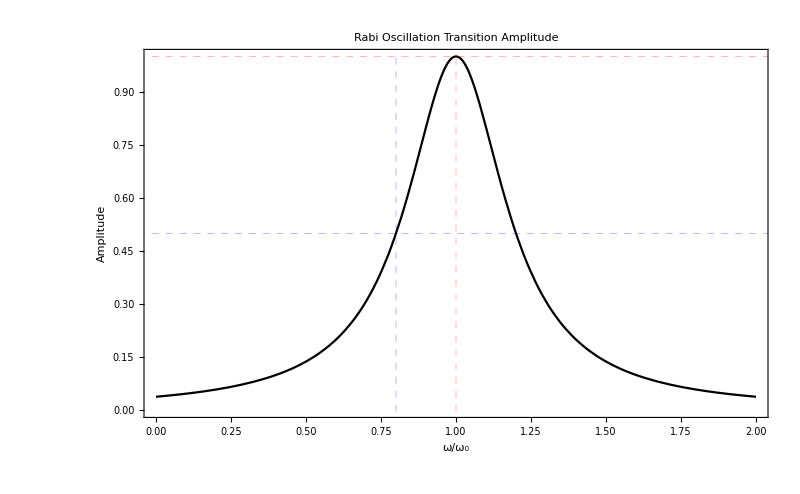

```mathematica
Plot[transAmp[k,0.1],{k,0,2},Frame->True,ImageSize->imgsize,PlotStyle->Black,LabelStyle->Black,FrameTicksStyle->Directive[Larger,FontSize->24],BaseStyle->{(*FontWeight->"Bold",*)FontSize->18},GridLines->{{{1,Directive[Red,Dashed]},{0.8,Directive[Blue,Dashed]}},{{transAmp[1,0.1],Directive[Red,Dashed]},{transAmp[0.8,0.1],Directive[Blue,Dashed]}}},PlotLabel->"Rabi Oscillation Transition Amplitude",FrameLabel->{"ω/ω_0","Amplitude"}]
```

```mathematica
Plot[{transProb[1,0.1,x],transProb[0.8,0.1,x]},{x,0,100},Frame->True,ImageSize->imgsize,PlotStyle->{Red,Blue},PlotLegends->Placed[{"ω/ω_0=1","ω/ω_0=0.8"},{Center,Above}],LabelStyle->Black,FrameTicksStyle->Directive[Larger,FontSize->24],BaseStyle->{(*FontWeight->"Bold",*)FontSize->18},GridLines->{None,{{1,Directive[Red,Dashed]},{transAmp[0.8,0.1],Directive[Blue,Dashed]}}},PlotLabel->"Rabi Oscillation Transition Probability",FrameLabel->{"ω_0 x","Transition Probability"}]
```

-Graphics-

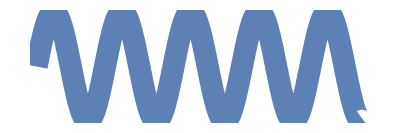

```mathematica
Plot[Sin[x],{x,0,30},AxesLabel->None,Axes->False,PlotStyle->Thickness[0.04],AspectRatio->1/3]
```